This is based on MWCPlot, originally developed for my presentation in London, but now redisigned (hopefully) to function with sliders as a “Manipulate” object in a CDF.

MWCPlot is quite general; any quantity resulting from the simulation can be plotted against any other resulting quantity. Here I assume that the x-axis will always be PO2, and that users would want to consider how all R, all T, or Y species vary with PO2. 

So here is my list of possible plots:

	0	Y vs. PO2
	1	fR vs. PO2
	2	R0, R1, R2, R3, R4, fR vs. PO2
	3	0 & 1
	4	0 & 2
	5	fT vs. PO2
	6	T0, T1, T2, T3, T4, fT vs PO2
	7	0 & 5
	8	0 & 6
	9	0, 1, 5
	10	0, 2, 6

Prior drafts of MWCGenGraph have been based on the idea of making base plots and combining them as required with Show commands.
I believe Show and PlotLegend do not work well together. For evidence, quit kernel, Evaluate Notebook MWC Implementation draft 1, then Evaluate Notebook scratchpad, and look into In/Out 53 through 55.

So I am redesigning MWCGenGraph so it is based on base datasets instead.

```mathematica
MWCGenGraph[
arg_, MWCDataSet_
] := Module[
{
DATASET,
OUTPUT,
i
},
DATASET = Which[

arg == 0, Transpose[
{#[[1]]&/@MWCDataSet,#[[3]]& /@ MWCDataSet}
],

arg == 1, Transpose[
{#[[1]]&/@MWCDataSet,#[[5]]& /@ MWCDataSet}
],

arg == 2, Prepend[
Table[
Transpose[
{
#[[1]] & /@ MWCDataSet,
#[[i]] &/@MWCDataSet
}
],
{i, {11,12,13,14,15}}
],
Transpose[
Prepend[
{#[[5]]& /@ MWCDataSet},
#[[1]] &/@ MWCDataSet
]
]
], 

arg == 3, Table[
Transpose[
{
#[[1]] & /@ MWCDataSet,
#[[i]] &/@MWCDataSet
}
],
{i, {3,5}}
],

arg == 4, Prepend[
Prepend[
Table[
Transpose[
{
#[[1]] & /@ MWCDataSet,
#[[i]] & /@ MWCDataSet
}
],
{i, {11, 12,13,14,15}}
],
Transpose[
{#[[1]] & /@ MWCDataSet,
#[[3]] & /@ MWCDataSet}
]
],
Transpose[
{#[[1]] & /@ MWCDataSet,
#[[5]] & /@ MWCDataSet}
]
],

arg == 5, Transpose[
{#[[1]]&/@MWCDataSet,#[[4]]& /@ MWCDataSet}
],

arg == 6, Prepend[
Table[
Transpose[
{
#[[1]] & /@ MWCDataSet,
#[[i]] &/@MWCDataSet
}
],
{i, Range[6,10]}
],
Transpose[
Prepend[
{#[[4]]& /@ MWCDataSet},
#[[1]] &/@ MWCDataSet
]
]
],

arg == 7, Table[
Transpose[
{
#[[1]] & /@ MWCDataSet,
#[[i]] &/@MWCDataSet
}
],
{i, {3,4}}
],

arg == 8, Prepend[
Prepend[
Table[
Transpose[
{
#[[1]] & /@ MWCDataSet,
#[[i]] & /@ MWCDataSet
}
],
{i, Range[6,10]}
],
Transpose[
{#[[1]] & /@ MWCDataSet,
#[[3]] & /@ MWCDataSet}
]
],
Transpose[
{#[[1]] & /@ MWCDataSet,
#[[4]] & /@ MWCDataSet}
]
],

arg == 9, Table[
Transpose[
{
#[[1]] & /@ mwcsolutionset,
#[[i]] & /@ mwcsolutionset
}
],
{i, Range[3,5]}
],

arg == 10, Prepend[
Prepend[
Prepend[
Table[
Transpose[
{
#[[1]] & /@ MWCDataSet,
#[[i]] & /@ MWCDataSet
}
],
{i, Range[6,15]}
],
Transpose[
{#[[1]] &/@ MWCDataSet,
#[[5]] & /@ MWCDataSet}
]
],
Transpose[
{#[[1]] &/@ MWCDataSet,
#[[4]] & /@ MWCDataSet}
]
],
Transpose[
{#[[1]] &/@ MWCDataSet,
#[[3]] & /@ MWCDataSet}
]
]
];
OUTPUT = ListPlot[
DATASET
]
]
```

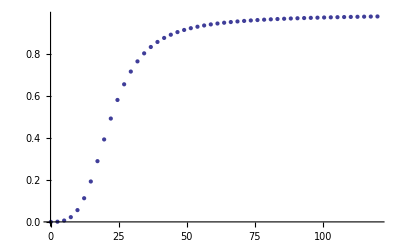
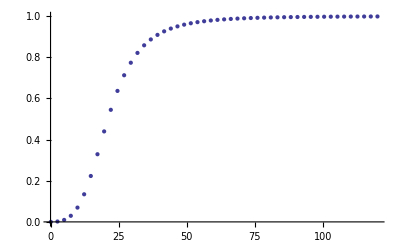
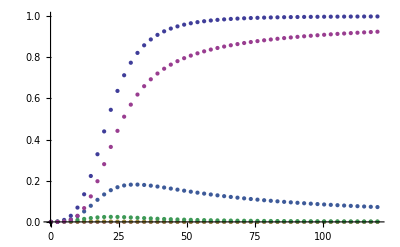
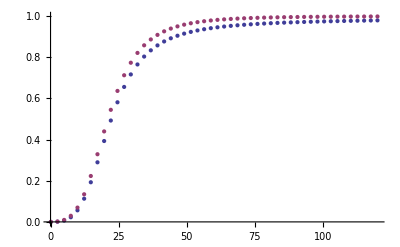
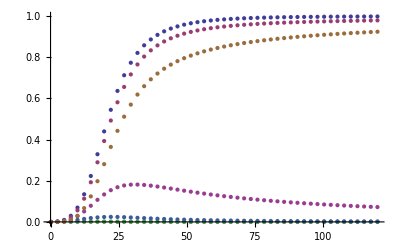
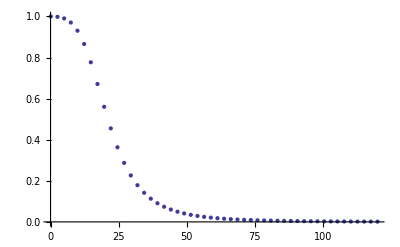
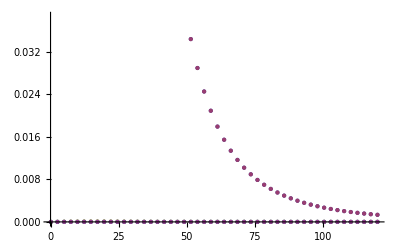
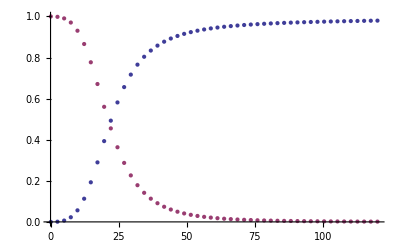

```mathematica
testset = Table[
MWCGenGraph[
i, mwcsolutionset
],
{i, 0, 10}
]
```